```mathematica
C30=IdentityMatrix[8];
C31={{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0}};
C32={{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0}};
C33={{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0}};
C34={{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0}};
C35={{1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,1,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,0,0,0,1,0},{0,0,0,1,0,0,0,0}};
C36={{1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0},{0,0,0,0,0,1,0,0}};

generators={{C31,C32,C33,C34,C35,C36}};

generators // MatrixForm
```

((1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0) | (1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0) | (1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0) | (1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0) | (1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0) | (1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0))

```mathematica
groupCNot3=PermutationGroup[{Cycles[{{5,7},{8,6}}],Cycles[{{5,6},{7,8}}],Cycles[{{7,3},{4,8}}],Cycles[{{4,3},{7,8}}],Cycles[{{2,6},{4,8}}],Cycles[{{6,8},{4,2}}]}];

(* 168 elements = 2^3 *3*7  *)
```

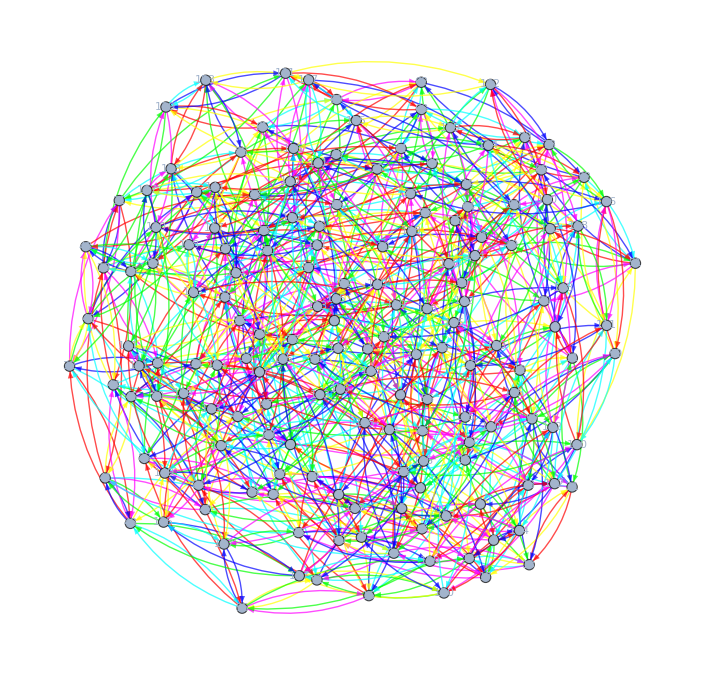

```mathematica
CayleyGraph[PermutationGroup[{Cycles[{{5,7},{8,6}}],Cycles[{{5,6},{7,8}}],Cycles[{{7,3},{4,8}}],Cycles[{{4,3},{7,8}}],Cycles[{{2,6},{4,8}}],Cycles[{{6,8},{4,2}}]}],VertexLabels->Placed["Name",Center],VertexSize->0.6]
```

```mathematica
GroupGenerators[groupCNot3]
```

{Cycles[{{5,7},{6,8}}],Cycles[{{5,6},{7,8}}],Cycles[{{3,7},{4,8}}],Cycles[{{3,4},{7,8}}],Cycles[{{2,6},{4,8}}],Cycles[{{2,4},{6,8}}]}

```mathematica
GroupElements[groupCNot3]
```

{Cycles[{}],Cycles[{{5,6},{7,8}}],Cycles[{{5,7},{6,8}}],Cycles[{{5,8},{6,7}}],Cycles[{{3,4},{7,8}}],Cycles[{{3,4},{5,6}}],Cycles[{{3,4},{5,7,6,8}}],Cycles[{{3,4},{5,8,6,7}}],Cycles[{{3,5},{4,6}}],Cycles[{{3,5,4,6},{7,8}}],Cycles[{{3,5,7},{4,6,8}}],Cycles[{{3,5,8},{4,6,7}}],Cycles[{{3,6,4,5},{7,8}}],Cycles[{{3,6},{4,5}}],Cycles[{{3,6,8},{4,5,7}}],Cycles[{{3,6,7},{4,5,8}}],Cycles[{{3,7,5},{4,8,6}}],Cycles[{{3,7,6},{4,8,5}}],Cycles[{{3,7},{4,8}}],Cycles[{{3,7,4,8},{5,6}}],Cycles[{{3,8,5},{4,7,6}}],Cycles[{{3,8,6},{4,7,5}}],Cycles[{{3,8},{4,7}}],Cycles[{{3,8,4,7},{5,6}}],Cycles[{{2,3},{6,7}}],Cycles[{{2,3},{5,6,8,7}}],Cycles[{{2,3},{5,7,8,6}}],Cycles[{{2,3},{5,8}}],Cycles[{{2,3,4},{6,7,8}}],Cycles[{{2,3,4},{5,6,8}}],Cycles[{{2,3,4},{5,7,6}}],Cycles[{{2,3,4},{5,8,7}}],Cycles[{{2,3,5},{4,7,6}}],Cycles[{{2,3,5,4,7,8,6}}],Cycles[{{2,3,5,6,8,4,7}}],Cycles[{{2,3,5,8},{4,7}}],Cycles[{{2,3,6,4,8,7,5}}],Cycles[{{2,3,6},{4,8,5}}],Cycles[{{2,3,6,7},{4,8}}],Cycles[{{2,3,6,5,7,4,8}}],Cycles[{{2,3,7,8,6,4,5}}],Cycles[{{2,3,7,6},{4,5}}],Cycles[{{2,3,7,4,5,6,8}}],Cycles[{{2,3,7},{4,5,8}}],Cycles[{{2,3,8,5},{4,6}}],Cycles[{{2,3,8,7,5,4,6}}],Cycles[{{2,3,8},{4,6,7}}],Cycles[{{2,3,8,4,6,5,7}}],Cycles[{{2,4,3},{6,8,7}}],Cycles[{{2,4,3},{5,6,7}}],Cycles[{{2,4,3},{5,7,8}}],Cycles[{{2,4,3},{5,8,6}}],Cycles[{{2,4},{6,8}}],Cycles[{{2,4},{5,6,7,8}}],Cycles[{{2,4},{5,7}}],Cycles[{{2,4},{5,8,7,6}}],Cycles[{{2,4,8,7,6,3,5}}],Cycles[{{2,4,8,6},{3,5}}],Cycles[{{2,4,8,3,5,6,7}}],Cycles[{{2,4,8},{3,5,7}}],Cycles[{{2,4,7,5},{3,6}}],Cycles[{{2,4,7,8,5,3,6}}],Cycles[{{2,4,7},{3,6,8}}],Cycles[{{2,4,7,3,6,5,8}}],Cycles[{{2,4,6,3,7,8,5}}],Cycles[{{2,4,6},{3,7,5}}],Cycles[{{2,4,6,8},{3,7}}],Cycles[{{2,4,6,5,8,3,7}}],Cycles[{{2,4,5},{3,8,6}}],Cycles[{{2,4,5,3,8,7,6}}],Cycles[{{2,4,5,6,7,3,8}}],Cycles[{{2,4,5,7},{3,8}}],Cycles[{{2,5,3},{4,6,7}}],Cycles[{{2,5,4,6,8,7,3}}],Cycles[{{2,5,7,8,4,6,3}}],Cycles[{{2,5,8,3},{4,6}}],Cycles[{{2,5},{4,7}}],Cycles[{{2,5,4,7},{6,8}}],Cycles[{{2,5,6},{4,7,8}}],Cycles[{{2,5,8},{4,7,6}}],Cycles[{{2,5},{3,4,8,7}}],Cycles[{{2,5,3,4,8,6,7}}],Cycles[{{2,5,6},{3,4,8}}],Cycles[{{2,5,7,6,3,4,8}}],Cycles[{{2,5,3,6,7,8,4}}],Cycles[{{2,5,4},{3,6,8}}],Cycles[{{2,5,7,4},{3,6}}],Cycles[{{2,5,8,7,3,6,4}}],Cycles[{{2,5},{3,7,8,4}}],Cycles[{{2,5,4,3,7,6,8}}],Cycles[{{2,5,6},{3,7,4}}],Cycles[{{2,5,8,6,4,3,7}}],Cycles[{{2,5},{3,8}}],Cycles[{{2,5,3,8},{6,7}}],Cycles[{{2,5,6},{3,8,7}}],Cycles[{{2,5,7},{3,8,6}}],Cycles[{{2,6,8,7,4,5,3}}],Cycles[{{2,6,7,3},{4,5}}],Cycles[{{2,6,4,5,7,8,3}}],Cycles[{{2,6,3},{4,5,8}}],Cycles[{{2,6,5},{4,8,7}}],Cycles[{{2,6,7},{4,8,5}}],Cycles[{{2,6},{4,8}}],Cycles[{{2,6,4,8},{5,7}}],Cycles[{{2,6,5},{3,4,7}}],Cycles[{{2,6,8,5,3,4,7}}],Cycles[{{2,6},{3,4,7,8}}],Cycles[{{2,6,3,4,7,5,8}}],Cycles[{{2,6,8,4},{3,5}}],Cycles[{{2,6,7,8,3,5,4}}],Cycles[{{2,6,4},{3,5,7}}],Cycles[{{2,6,3,5,8,7,4}}],Cycles[{{2,6,5},{3,7,8}}],Cycles[{{2,6,8},{3,7,5}}],Cycles[{{2,6},{3,7}}],Cycles[{{2,6,3,7},{5,8}}],Cycles[{{2,6,5},{3,8,4}}],Cycles[{{2,6,7,5,4,3,8}}],Cycles[{{2,6},{3,8,7,4}}],Cycles[{{2,6,4,3,8,5,7}}],Cycles[{{2,7,4,8,6,5,3}}],Cycles[{{2,7,3},{4,8,5}}],Cycles[{{2,7,6,3},{4,8}}],Cycles[{{2,7,5,6,4,8,3}}],Cycles[{{2,7,4,5},{6,8}}],Cycles[{{2,7},{4,5}}],Cycles[{{2,7,8},{4,5,6}}],Cycles[{{2,7,6},{4,5,8}}],Cycles[{{2,7,3,4,6,8,5}}],Cycles[{{2,7},{3,4,6,5}}],Cycles[{{2,7,8},{3,4,6}}],Cycles[{{2,7,5,8,3,4,6}}],Cycles[{{2,7,6,8,4,3,5}}],Cycles[{{2,7,8},{3,5,4}}],Cycles[{{2,7},{3,5,6,4}}],Cycles[{{2,7,4,3,5,8,6}}],Cycles[{{2,7,5},{3,6,8}}],Cycles[{{2,7,8},{3,6,5}}],Cycles[{{2,7},{3,6}}],Cycles[{{2,7,3,6},{5,8}}],Cycles[{{2,7,6,5,3,8,4}}],Cycles[{{2,7,5,4},{3,8}}],Cycles[{{2,7,4},{3,8,6}}],Cycles[{{2,7,3,8,5,6,4}}],Cycles[{{2,8,5,3},{4,7}}],Cycles[{{2,8,6,5,4,7,3}}],Cycles[{{2,8,3},{4,7,6}}],Cycles[{{2,8,4,7,5,6,3}}],Cycles[{{2,8,5},{4,6,7}}],Cycles[{{2,8,7},{4,6,5}}],Cycles[{{2,8},{4,6}}],Cycles[{{2,8,4,6},{5,7}}],Cycles[{{2,8,6,7,3,4,5}}],Cycles[{{2,8,7},{3,4,5}}],Cycles[{{2,8},{3,4,5,6}}],Cycles[{{2,8,3,4,5,7,6}}],Cycles[{{2,8,3,5},{6,7}}],Cycles[{{2,8},{3,5}}],Cycles[{{2,8,7},{3,5,6}}],Cycles[{{2,8,6},{3,5,7}}],Cycles[{{2,8,4,3,6,7,5}}],Cycles[{{2,8},{3,6,5,4}}],Cycles[{{2,8,7},{3,6,4}}],Cycles[{{2,8,5,7,4,3,6}}],Cycles[{{2,8,4},{3,7,5}}],Cycles[{{2,8,3,7,6,5,4}}],Cycles[{{2,8,6,4},{3,7}}],Cycles[{{2,8,5,6,3,7,4}}]}

```mathematica
aa = PermutationGroup[{Cycles[{{2,7,3,8,5,6,4}}],Cycles[{{3,4},{7,8}}]}];
Length[GroupElements[aa]]
Length[GroupElements[groupCNot3]]
GroupElements[aa]
```

168

168

{Cycles[{}],Cycles[{{5,6},{7,8}}],Cycles[{{5,7},{6,8}}],Cycles[{{5,8},{6,7}}],Cycles[{{3,4},{7,8}}],Cycles[{{3,4},{5,6}}],Cycles[{{3,4},{5,7,6,8}}],Cycles[{{3,4},{5,8,6,7}}],Cycles[{{3,5},{4,6}}],Cycles[{{3,5,4,6},{7,8}}],Cycles[{{3,5,7},{4,6,8}}],Cycles[{{3,5,8},{4,6,7}}],Cycles[{{3,6,4,5},{7,8}}],Cycles[{{3,6},{4,5}}],Cycles[{{3,6,8},{4,5,7}}],Cycles[{{3,6,7},{4,5,8}}],Cycles[{{3,7,5},{4,8,6}}],Cycles[{{3,7,6},{4,8,5}}],Cycles[{{3,7},{4,8}}],Cycles[{{3,7,4,8},{5,6}}],Cycles[{{3,8,5},{4,7,6}}],Cycles[{{3,8,6},{4,7,5}}],Cycles[{{3,8},{4,7}}],Cycles[{{3,8,4,7},{5,6}}],Cycles[{{2,3},{6,7}}],Cycles[{{2,3},{5,6,8,7}}],Cycles[{{2,3},{5,7,8,6}}],Cycles[{{2,3},{5,8}}],Cycles[{{2,3,4},{6,7,8}}],Cycles[{{2,3,4},{5,6,8}}],Cycles[{{2,3,4},{5,7,6}}],Cycles[{{2,3,4},{5,8,7}}],Cycles[{{2,3,5},{4,7,6}}],Cycles[{{2,3,5,4,7,8,6}}],Cycles[{{2,3,5,6,8,4,7}}],Cycles[{{2,3,5,8},{4,7}}],Cycles[{{2,3,6,4,8,7,5}}],Cycles[{{2,3,6},{4,8,5}}],Cycles[{{2,3,6,7},{4,8}}],Cycles[{{2,3,6,5,7,4,8}}],Cycles[{{2,3,7,8,6,4,5}}],Cycles[{{2,3,7,6},{4,5}}],Cycles[{{2,3,7,4,5,6,8}}],Cycles[{{2,3,7},{4,5,8}}],Cycles[{{2,3,8,5},{4,6}}],Cycles[{{2,3,8,7,5,4,6}}],Cycles[{{2,3,8},{4,6,7}}],Cycles[{{2,3,8,4,6,5,7}}],Cycles[{{2,4,3},{6,8,7}}],Cycles[{{2,4,3},{5,6,7}}],Cycles[{{2,4,3},{5,7,8}}],Cycles[{{2,4,3},{5,8,6}}],Cycles[{{2,4},{6,8}}],Cycles[{{2,4},{5,6,7,8}}],Cycles[{{2,4},{5,7}}],Cycles[{{2,4},{5,8,7,6}}],Cycles[{{2,4,8,7,6,3,5}}],Cycles[{{2,4,8,6},{3,5}}],Cycles[{{2,4,8,3,5,6,7}}],Cycles[{{2,4,8},{3,5,7}}],Cycles[{{2,4,7,5},{3,6}}],Cycles[{{2,4,7,8,5,3,6}}],Cycles[{{2,4,7},{3,6,8}}],Cycles[{{2,4,7,3,6,5,8}}],Cycles[{{2,4,6,3,7,8,5}}],Cycles[{{2,4,6},{3,7,5}}],Cycles[{{2,4,6,8},{3,7}}],Cycles[{{2,4,6,5,8,3,7}}],Cycles[{{2,4,5},{3,8,6}}],Cycles[{{2,4,5,3,8,7,6}}],Cycles[{{2,4,5,6,7,3,8}}],Cycles[{{2,4,5,7},{3,8}}],Cycles[{{2,5,3},{4,6,7}}],Cycles[{{2,5,4,6,8,7,3}}],Cycles[{{2,5,7,8,4,6,3}}],Cycles[{{2,5,8,3},{4,6}}],Cycles[{{2,5},{4,7}}],Cycles[{{2,5,4,7},{6,8}}],Cycles[{{2,5,6},{4,7,8}}],Cycles[{{2,5,8},{4,7,6}}],Cycles[{{2,5},{3,4,8,7}}],Cycles[{{2,5,3,4,8,6,7}}],Cycles[{{2,5,6},{3,4,8}}],Cycles[{{2,5,7,6,3,4,8}}],Cycles[{{2,5,3,6,7,8,4}}],Cycles[{{2,5,4},{3,6,8}}],Cycles[{{2,5,7,4},{3,6}}],Cycles[{{2,5,8,7,3,6,4}}],Cycles[{{2,5},{3,7,8,4}}],Cycles[{{2,5,4,3,7,6,8}}],Cycles[{{2,5,6},{3,7,4}}],Cycles[{{2,5,8,6,4,3,7}}],Cycles[{{2,5},{3,8}}],Cycles[{{2,5,3,8},{6,7}}],Cycles[{{2,5,6},{3,8,7}}],Cycles[{{2,5,7},{3,8,6}}],Cycles[{{2,6,8,7,4,5,3}}],Cycles[{{2,6,7,3},{4,5}}],Cycles[{{2,6,4,5,7,8,3}}],Cycles[{{2,6,3},{4,5,8}}],Cycles[{{2,6,5},{4,8,7}}],Cycles[{{2,6,7},{4,8,5}}],Cycles[{{2,6},{4,8}}],Cycles[{{2,6,4,8},{5,7}}],Cycles[{{2,6,5},{3,4,7}}],Cycles[{{2,6,8,5,3,4,7}}],Cycles[{{2,6},{3,4,7,8}}],Cycles[{{2,6,3,4,7,5,8}}],Cycles[{{2,6,8,4},{3,5}}],Cycles[{{2,6,7,8,3,5,4}}],Cycles[{{2,6,4},{3,5,7}}],Cycles[{{2,6,3,5,8,7,4}}],Cycles[{{2,6,5},{3,7,8}}],Cycles[{{2,6,8},{3,7,5}}],Cycles[{{2,6},{3,7}}],Cycles[{{2,6,3,7},{5,8}}],Cycles[{{2,6,5},{3,8,4}}],Cycles[{{2,6,7,5,4,3,8}}],Cycles[{{2,6},{3,8,7,4}}],Cycles[{{2,6,4,3,8,5,7}}],Cycles[{{2,7,4,8,6,5,3}}],Cycles[{{2,7,3},{4,8,5}}],Cycles[{{2,7,6,3},{4,8}}],Cycles[{{2,7,5,6,4,8,3}}],Cycles[{{2,7,4,5},{6,8}}],Cycles[{{2,7},{4,5}}],Cycles[{{2,7,8},{4,5,6}}],Cycles[{{2,7,6},{4,5,8}}],Cycles[{{2,7,3,4,6,8,5}}],Cycles[{{2,7},{3,4,6,5}}],Cycles[{{2,7,8},{3,4,6}}],Cycles[{{2,7,5,8,3,4,6}}],Cycles[{{2,7,6,8,4,3,5}}],Cycles[{{2,7,8},{3,5,4}}],Cycles[{{2,7},{3,5,6,4}}],Cycles[{{2,7,4,3,5,8,6}}],Cycles[{{2,7,5},{3,6,8}}],Cycles[{{2,7,8},{3,6,5}}],Cycles[{{2,7},{3,6}}],Cycles[{{2,7,3,6},{5,8}}],Cycles[{{2,7,6,5,3,8,4}}],Cycles[{{2,7,5,4},{3,8}}],Cycles[{{2,7,4},{3,8,6}}],Cycles[{{2,7,3,8,5,6,4}}],Cycles[{{2,8,5,3},{4,7}}],Cycles[{{2,8,6,5,4,7,3}}],Cycles[{{2,8,3},{4,7,6}}],Cycles[{{2,8,4,7,5,6,3}}],Cycles[{{2,8,5},{4,6,7}}],Cycles[{{2,8,7},{4,6,5}}],Cycles[{{2,8},{4,6}}],Cycles[{{2,8,4,6},{5,7}}],Cycles[{{2,8,6,7,3,4,5}}],Cycles[{{2,8,7},{3,4,5}}],Cycles[{{2,8},{3,4,5,6}}],Cycles[{{2,8,3,4,5,7,6}}],Cycles[{{2,8,3,5},{6,7}}],Cycles[{{2,8},{3,5}}],Cycles[{{2,8,7},{3,5,6}}],Cycles[{{2,8,6},{3,5,7}}],Cycles[{{2,8,4,3,6,7,5}}],Cycles[{{2,8},{3,6,5,4}}],Cycles[{{2,8,7},{3,6,4}}],Cycles[{{2,8,5,7,4,3,6}}],Cycles[{{2,8,4},{3,7,5}}],Cycles[{{2,8,3,7,6,5,4}}],Cycles[{{2,8,6,4},{3,7}}],Cycles[{{2,8,5,6,3,7,4}}]}